```mathematica
pivot[iStar_, jStar_, tableau_] := (
newTableau = tableau;
numberRows = Dimensions[tableau][[1]];
numberCols = Dimensions[tableau][[2]];
(* switch row tableau variables *)
newTableau[[1,jStar]] = tableau[[iStar, numberCols]];
newTableau[[iStar, numberCols]] = tableau[[1,jStar]];
(* switch column tableau variables *)
newTableau[[numberRows,jStar]] = -tableau[[iStar, 1]];
newTableau[[iStar, 1]] = -tableau[[numberRows,jStar]];
(* adjust loop bounds to skip 1st column and last row *)
For[ii = 2, ii < numberRows, ii++,
For[jj=2,jj<numberCols,jj++,
If[ii == iStar && jj == jStar, 
newTableau[[ii,jj]]=1/tableau[[iStar, jStar]]];
If[ii== iStar && jj ≠ jStar,
newTableau[[ii,jj]]= -tableau[[iStar, jj]]/tableau[[iStar, jStar]]];
If[ii ≠ iStar && jj == jStar,
newTableau[[ii, jj]]= tableau[[ii, jStar]]/tableau[[iStar, jStar]]];
If[ii ≠ iStar && jj ≠ jStar,
newTableau[[ii,jj]] = tableau[[ii,jj]]-tableau[[iStar,jj]]*tableau[[ii, jStar]]/tableau[[iStar,jStar]]];
]
];
Return[newTableau];
)
```

```mathematica
g1[x1_,x2_]:=20x1+15x2;b1=500;
g2[x1_,x2_]:=10x1+20x2;b2=400;
g3[x1_,x2_]:=1x1+0x2;b3=25;
g3grph[x1_,x2_]:=1*10^6x1+1x2;b3grph=25*10^6;
g4[x1_,x2_]:=0x1+1x2;b4=20;

p1=9; (* $9 whether buying or selling *)
p2=22.50;(* $15 for the first 400hrs *)
initialResourceCost=4500+6000;
```

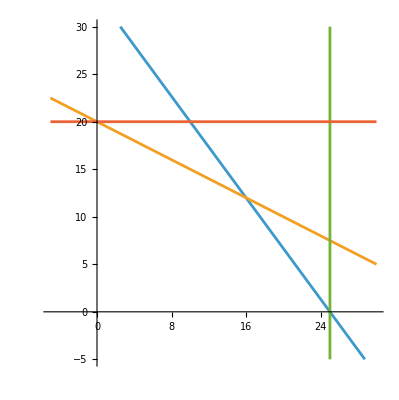

```mathematica
g1[x1_]=x2/.Solve[g1[x1,x2]==b1][[1,1]];
g2[x1_]=x2/.Solve[g2[x1,x2]==b2][[1,1]];
g3[x1_]=x2/.Solve[g3grph[x1,x2]==b3grph][[1,1]];
g4[x1_]=x2/.Solve[g4[x1,x2]==b4][[1,1]];Plot[{g1[x],g2[x],g3[x],g4[x]},{x,-5,30},AspectRatio->Automatic,PlotHighlighting->None,PlotRange->{-5,30}]
```

```mathematica
a0 = {"", "y1", "y2","y3","y4", 1, ""};
a1 = {"x1", 20, 10,1 ,0,-500, "v1"};
a2 = {"x2", 15, 20,0,1,-750, "v2"};
aObj = {-1, 500, 400,25,20, -10500, "w->min"};
aLast = {"", -"s1", -"s2", -"s3",-"s4",-"z->min", ""};
a={a0,a1,a2,aObj,aLast};
Print["a = ",MatrixForm[a] ]
```

a = ( | y1 | y2 | y3 | y4 | 1 | 
x1 | 20 | 10 | 1 | 0 | -500 | v1
x2 | 15 | 20 | 0 | 1 | -750 | v2
-1 | 500 | 400 | 25 | 20 | -10500 | w->min
 | -s1 | -s2 | -s3 | -s4 | -z->min | )

```mathematica
b = pivot[2,2,a]
Print["b = ", MatrixForm[b]]
```

{{,v1,y2,y3,y4,1,},{s1,1/20,-1/2,-1/20,0,25,y1},{x2,3/4,25/2,-3/4,1,-375,v2},{-1,25,150,0,20,2000,w->min},{,-x1,-s2,-s3,-s4,-z->min,}}

b = ( | v1 | y2 | y3 | y4 | 1 | 
s1 | 1/20 | -1/2 | -1/20 | 0 | 25 | y1
x2 | 3/4 | 25/2 | -3/4 | 1 | -375 | v2
-1 | 25 | 150 | 0 | 20 | 2000 | w->min
 | -x1 | -s2 | -s3 | -s4 | -z->min | )

```mathematica
c = pivot[2,3, b]
Print["c = ", MatrixForm[c]]
```

{{,v1,y1,y3,y4,1,},{s2,1/10,-2,-1/10,0,50,y2},{x2,2,-25,-2,1,250,v2},{-1,40,-300,-15,20,9500,w->min},{,-x1,-s1,-s3,-s4,-z->min,}}

c = ( | v1 | y1 | y3 | y4 | 1 | 
s2 | 1/10 | -2 | -1/10 | 0 | 50 | y2
x2 | 2 | -25 | -2 | 1 | 250 | v2
-1 | 40 | -300 | -15 | 20 | 9500 | w->min
 | -x1 | -s1 | -s3 | -s4 | -z->min | )

```mathematica
d = pivot[3,3,c]
Print["d = ", MatrixForm[d]]
```

{{,v1,v2,y3,y4,1,},{s2,-3/50,2/25,3/50,-2/25,30,y2},{s1,2/25,-1/25,-2/25,1/25,10,y1},{-1,16,12,9,8,6500,w->min},{,-x1,-x2,-s3,-s4,-z->min,}}

d = ( | v1 | v2 | y3 | y4 | 1 | 
s2 | -3/50 | 2/25 | 3/50 | -2/25 | 30 | y2
s1 | 2/25 | -1/25 | -2/25 | 1/25 | 10 | y1
-1 | 16 | 12 | 9 | 8 | 6500 | w->min
 | -x1 | -x2 | -s3 | -s4 | -z->min | )

```mathematica
xStar1Base = 16; xStar2Base = 12; xStarBase ={xStar1Base, xStar2Base}; 
yStar1Base = 10; yStar2Base = 30; yStarBase = {yStar1Base, yStar2Base};
(*part b: Should the company have any extra material delivered without scheduling any overtime? If so, how much?*)
(*We want positive ROI. We can examine it through the dual solution. Y1 = 10, and $9/lb of material, so we should buy more.*)
(*We should move our material constraint up to the intersection between the labor constraint and demand of x1.*)
(*We know this because of the following changes in material constraints.*)
Solve[g2[u,v] == b2 && g3[u,v] == b3]
```

{{u→25,v→15/2}}

```mathematica
b1b = g1[25, 15/2]; 
db1b = b1b - b1;
Print[db1b]
```

225/2

```mathematica
(*12.2 b ans: buy 225/2 lbs of material zb = 6500 + (y1-p1)db1 = 6612.50*)

(*12.2 c Should the company schedule overtime if we take action in b? We need to include changes in material constraints (and resulting profits). *)
(* y2 = 30 > 22.50 = p2 => yes, schedule overtime *)
Solve[g1[u,v]==b1max&&g4[u,v]==b4]
b2c=g2[125/8,20]
db2c=b2c-b2
```

{{u→-15+b1max/20,v→20}}

2225/4

625/4

```mathematica
(* 12.2c ans: schedule 625/4 = 156.25hrs overtime 
extra info:xc=(125/8,20) 
zc=6612.5+(y2-p2)*db2=6612.5+(30-22.50)(625/4)=7784.38 *)
6612.5+(30-22.50)(625/4)
```

```mathematica
7784.375
(* Part d:
From graph: buying material and labor (b1&b2) will remain profitable until demand for both products is reach at (x1,x2)=(25,20)*)
```

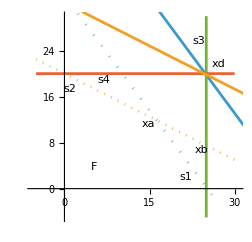

```mathematica
(*We basically want the largest feasible region possible in this situation. That is because we make money on each extra lb of material produced and each extra hour worked by laborers. This goes on until we meet demand problems.*)
b1d = g1[25,20]
b2d = g2[25,20]
db1d = b1d - b1
db2d = b2d - b2 
db1dCost = db1d*p1
db2dCost = db2d*p2 
totalInvestmentDCost = db1dCost + db2dCost
```

800

650

300

250

2700

5625.

8325.